## File informations

```mathematica
(*Clear all values*) 
ClearAll["`*"]


(*Set rawdata folder and output data folder*) 
dir=SetDirectory[NotebookDirectory[]];
```

```mathematica
(*Filename of rawdata*)
filename="AVG.xlsx";
```

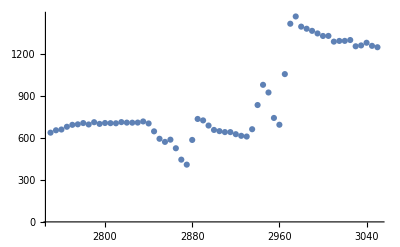

```mathematica
(*Import data and Remove comment line*)
raw=Import[filename][[1]];
data=Transpose[Transpose[Drop[raw,1]][[1;;2]]];
SD=Transpose[Drop[raw,1]][[3]];
ListPlot[data]
```

## SFG model

```mathematica
(*Number of peak*)
PkNo=6;


(*Fittinh model*)
S[1]=a1/((w-w1)+ⅈ f1);
S[2]=a2/((w-w2)+ⅈ f2);
S[3]=a3/((w-w3)+ⅈ f3);
S[4]=a4/((w-w4)+ⅈ f4);
S[5]=a5/((w-w5)+ⅈ f5);
S[6]=a6/((w-w6)+ⅈ f6);
NR=n ⅇ^(-ⅈ p);
SFG=Abs[(NR+∑_(i=1)^PkNo S[i])]^2;

(*Type variables*)
variables={
n,p,
a1,a2,a3,a4,a5,a6,
w1,w2,w3,w4,w5,w6,
f1,f2,f3,f4,f5,f6
};
```

```mathematica
(*Build your initial parameter*)
Initialvalues={
31.7,5.57,
16.6,73.2,82,182.5,-31.6,60.6,
2854.2,2876.9,2907.3,2938.7,2946.6,2962.8,
7.26,8.3,19.2,15.8,7.1,4.9
};
```

## SFG simulation

### Code for SFG simulation program

```mathematica
Manipulate[
Grid[{
{Panel[
Show[Plot[SFG/.{
n->Initial[[1]],p->Initial[[2]],
a1->Initial[[3]],a2->Initial[[4]],a3->Initial[[5]],a4->Initial[[6]],a5->Initial[[7]],a6->Initial[[8]],
w1->Initial[[9]],w2->Initial[[10]],w3->Initial[[11]],w4->Initial[[12]],w5->Initial[[13]],w6->Initial[[14]],
f1->Initial[[15]],f2->Initial[[16]],f3->Initial[[17]],f4->Initial[[18]],f5->Initial[[19]],f6->Initial[[20]]
},{w,data[[1,1]], data[[-1,1]]},PlotRange-> All,PlotStyle->Red,ImageSize->650],
ListPlot[data]]
]},

{"constraints"Panel[
constraints=Module[{table},
table=Table[
Which[
EnableLL[[i]]==True&&EnableUL[[i]]==True,LL[[i]]<variables[[i]]<UL[[i]],
EnableLL[[i]]==True&&EnableUL[[i]]==False,LL[[i]]<variables[[i]],
EnableLL[[i]]==False&&EnableUL[[i]]==True,variables[[i]]<UL[[i]],
EnableLL[[i]]==False&&EnableUL[[i]]==False,false
],{i,1,Length[variables]}];
Delete[table,Position[table,false]]]]},

{"initialparameter"Panel[
initialparameter=Table[
variables[[i]]->Initial[[i]],{i,1,Length[variables]}]
]
}
}],


{LL,{Initialvalues-5},ControlType->None},
{EnableLL,{Table[True,{Length[variables]}]},ControlType->None},
{Initial,{Initialvalues},ControlType->None},
{EnableUL,{Table[True,{Length[variables]}]},ControlType->None},
{UL,{Initialvalues+5},ControlType->None},

Panel[Grid[Transpose[{

Prepend[variables,"variable"],
Prepend[Outer[InputField[Dynamic[LL[[#1]]],FieldSize->4,Enabled->Dynamic[EnableLL[[#1]]]]&,Range[Length[variables]]],"LL"],
Prepend[Outer[Checkbox[Dynamic[EnableLL[[#1]]],{False,True}]&,Range[Length[variables]]],"<"],

Prepend[Outer[Slider[Dynamic[Initial[[#1]]],{Dynamic[LL[[#1]]],Dynamic[UL[[#1]]]},ImageSize->100]&,Range[Length[variables]]],"Initial"],
Prepend[Outer[Panel[Dynamic[Initial[[#1]]]]&,Range[Length[variables]]],""],

Prepend[Outer[Checkbox[Dynamic[EnableUL[[#1]]],{False,True}]&,Range[Length[variables]]],"<"],
Prepend[Outer[InputField[Dynamic[UL[[#1]]],FieldSize->4,Enabled->Dynamic[EnableUL[[#1]]]]&,Range[Length[variables]]],"UL"]
}]]],
ControlPlacement->Left
]
```

## SFG fitting

### Fit

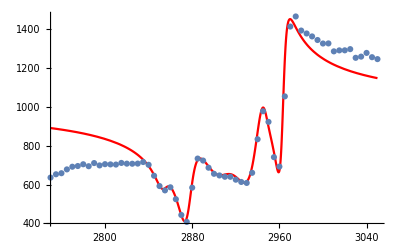

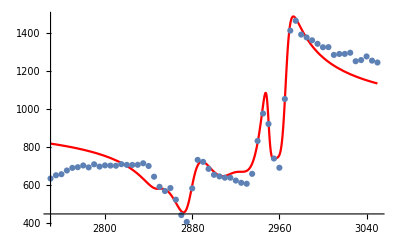

| Estimate | Standard Error | t-Statistic | P-Value
n | 30.8884 | 0.646907 | 47.7478 | 1.45506×10^-37
p | 5.77559 | 0.233001 | 24.7879 | 2.68782×10^-26
a1 | 21.6 | 68.8955 | 0.313518 | 0.755477
a2 | 78.2 | 87.3509 | 0.89524 | 0.375885
a3 | 87. | 279.592 | 0.311168 | 0.75725
a4 | 187.5 | 261.251 | 0.717702 | 0.477011
a5 | -26.6 | 171.111 | -0.155455 | 0.877226
a6 | 65.6 | 49.0933 | 1.33623 | 0.188843
w1 | 2849.2 | 18.5659 | 153.464 | 3.26226×10^-58
w2 | 2878.16 | 4.5563 | 631.688 | 2.15511×10^-83
w3 | 2912.3 | 17.1692 | 169.624 | 5.41512×10^-60
w4 | 2943.7 | 25.2503 | 116.581 | 2.49517×10^-53
w5 | 2949.66 | 1.36642 | 2158.67 | 2.83936×10^-105
w6 | 2965.34 | 1.33738 | 2217.27 | 9.46977×10^-106
f1 | 12.26 | 34.756 | 0.352744 | 0.726087
f2 | 10.6264 | 10.2003 | 1.04177 | 0.303621
f3 | 20.8377 | 37.2492 | 0.559414 | 0.578923
f4 | 18.406 | 19.021 | 0.967664 | 0.338886
f5 | 3.77746 | 20.8073 | 0.181544 | 0.856835
f6 | 6.35888 | 2.11963 | 2.99999 | 0.00457685

R^2 0.996028

0.996028-R[2]

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
n | 30.8884 | 0.646906 | 47.7479 | 1.455×10^-37
p | 5.77559 | 0.233 | 24.7879 | 2.68766×10^-26
a1 | 21.6 | 68.8955 | 0.313518 | 0.755476
a2 | 78.2 | 87.3509 | 0.89524 | 0.375885
a3 | 87. | 279.592 | 0.311168 | 0.757249
a4 | 187.5 | 261.25 | 0.717703 | 0.47701
a5 | -26.6 | 171.111 | -0.155455 | 0.877225
a6 | 65.6 | 49.0932 | 1.33623 | 0.188842
w1 | 2849.2 | 18.5659 | 153.465 | 3.26224×10^-58
w2 | 2878.16 | 4.5563 | 631.688 | 2.1551×10^-83
w3 | 2912.3 | 17.1691 | 169.624 | 5.41467×10^-60
w4 | 2943.7 | 25.2503 | 116.581 | 2.49492×10^-53
w5 | 2949.66 | 1.36642 | 2158.68 | 2.83906×10^-105
w6 | 2965.34 | 1.33738 | 2217.27 | 9.4689×10^-106
f1 | 12.26 | 34.756 | 0.352745 | 0.726087
f2 | 10.6264 | 10.2003 | 1.04177 | 0.30362
f3 | 20.8377 | 37.2491 | 0.559414 | 0.578922
f4 | 18.4059 | 19.021 | 0.967665 | 0.338886
f5 | 3.77746 | 20.8073 | 0.181545 | 0.856835
f6 | 6.35888 | 2.11963 | 3. | 0.00457678

R^2 0.996028

-3.55271×10^-15

{26.7<n<36.7,0.57<p<10.57,11.6<a1<21.6,68.2<a2<78.2,77<a3<87,177.5<a4<187.5,-36.6<a5<-26.6,55.6<a6<65.6,2849.2<w1<2859.2,2871.9<w2<2881.9,2902.3<w3<2912.3,2933.7<w4<2943.7,2941.6<w5<2951.6,2957.8<w6<2967.8,2.26<f1<12.26,3.3<f2<13.3,14.2<f3<24.2,10.8<f4<20.8,2.1<f5<12.1,-0.1<f6<9.9}

```mathematica
(*Set intermidiate output parameter as a initial parameter for next loop*)
changep=Table[variables[[i]]->ToExpression[StringJoin["p",ToString[#]]&/@variables][[i]],{i,1,Length[variables]}];
initial=initialparameter/.changep;


(*Construct initial parameter table*)
parameter=Table[{variables[[i]],ToExpression[StringJoin["p",ToString[#]]&/@variables][[i]]},{i,1,Length[variables]}];

(*Plot with initial parameters*)
Show[Plot[SFG/.initialparameter,{w,data[[1,1]], data[[-1,1]]},PlotRange-> All,PlotStyle->Red],ListPlot[data]]

(*Plot the fitting result of each loop*)
plotresult[i_]:=Show[Plot[SFG/.bestfitparameters[i],{w,data[[1,1]], data[[-1,1]]},PlotRange-> All,PlotStyle->Red],ListPlot[data]];


TEST=1;
Quiet[While[Abs[TEST]>10^-10,
Do[
fit=NonlinearModelFit[data,{SFG,constraints},parameter/.initial,w,Weights->1/SD^2,MaxIterations->100];
initial=fit["BestFitParameters"]/.changep;
bestfitparameters[i]=fit["BestFitParameters"];
Print[]; 
Print[]; 
Print[plotresult[i]];
Print[parametertable[i]=fit["ParameterTable"]];
Print[R^2,R[i]=fit["RSquared"]];
Print[TEST=R[1]-R[2]];
,{i,2}]]];
constraints
```

## Save Data

```mathematica
(*Set output subfolder*)
Quiet[outdir=StringJoin[dir]];

(*Construct fit table*)
fitdata=Join[{"fitdata"},Table[SFG/.fit["BestFitParameters"],{w,Transpose[data][[1]]}]];

(*Save dataset*)
Export[StringJoin[outdir,"\\",StringDrop[filename,-5],"-plot.csv"],Transpose[Join[{raw[[All,1]],raw[[All,2]],raw[[All,3]],fitdata}]]]

(*Save fitting parameters*)
Quiet[Export[StringJoin[outdir,"\\",StringDrop[filename,-5],"-fit.csv"],Partition[Join[Flatten[fit["ParameterTable"][[1,1]]],{R^2,fit["RSquared"],"","",""}],5]]]
```

C:\Users\Joonhee\Desktop\New folder\AVG-plot.csv

C:\Users\Joonhee\Desktop\New folder\AVG-fit.csv